# Cavendish Example Notebook

## 1. Determining the Variation in a Laser Spot’s Location

### Our goal here is to import a series of images of a laser spot on a wall and then use Mathematica to determine where the center of the laser spot is and figure out how/if the laser is moving between pulses. The first thing that we want to do is be able to import our data to Mathematica. Here, we are importing a single image from our directory as a test to make sure we are doing this correctly.

```mathematica
imgTest = Import["C:\\Users\\steve\\Desktop\\Lab 02 Images\\Lab 02 Images\\01.jpg"]
```

-Graphics-

### We have successfully imported a single image. As we can see there is a lot more information here than just the laser spot that we want. Our goal now is to filter out all the excess information in the image that is NOT the laser spot. We can use the Binarize command to do this.

```mathematica
binTest=Binarize[imgTest,0.98]
```

-Graphics-

### Now that we have binarized our original image, we can see where the laser spot is located, but there are also some bright spots elsewhere in the image that are not from our laser . We want to get rid of those, so we will use the DeleteSmallComponents command to get rid of bright spots that are much smaller than our laser spot is .

```mathematica
binNewTest=DeleteSmallComponents[binTest,50]
```

-Graphics-

### Now that we have successfully isolated our laser spot, we want to determine where the center of the spot is located. To do this, we use the ComponentMeasurements command.

```mathematica
centerTest=ComponentMeasurements[binNewTest,"Centroid"]
```

{1→{884.439,748.433}}

### We can also do this in a single command, performing all our necessary tasks at once. This will come in handy when we implement this procedure on a set of images.

```mathematica
singleTest=ComponentMeasurements[DeleteSmallComponents[Binarize[Import["C:\\Users\\steve\\Desktop\\Lab 02 Images\\Lab 02 Images\\01.jpg"],0.98],50],"Centroid"]
```

{1→{884.439,748.433}}

### Now that we have shown then capability to perform this on a single image, lets repeat the process for all 40 images that we have in our dataset . First we need to set our directory which will save us typing later on .

```mathematica
SetDirectory["C:\\Users\\steve\\Desktop\\Lab 02 Images\\Lab 02 Images"];
```

### Now we want to create an array that holds the names of all of our images . Because we have previously set our directory, we just have to call the name of the file during our Import command, which we can do by calling back to this array .

```mathematica
list=FileNames[]
```

{01.jpg,02.jpg,03.jpg,04.jpg,05.jpg,06.jpg,07.jpg,08.jpg,09.jpg,10.jpg,11.jpg,12.jpg,13.jpg,14.jpg,15.jpg,16.jpg,17.jpg,18.jpg,19.jpg,20.jpg,21.jpg,22.jpg,23.jpg,24.jpg,25.jpg,26.jpg,27.jpg,28.jpg,29.jpg,30.jpg,31.jpg,32.jpg,33.jpg,34.jpg,35.jpg,36.jpg,37.jpg,38.jpg,39.jpg,40.jpg}

```mathematica
"01.jpg"
```

01.jpg

### Testing our code from earlier on "01.jpg" which is the initial test image we used .

```mathematica
ComponentMeasurements[DeleteSmallComponents[Binarize[Import[
"01.jpg"],0.98],50],"Centroid"]
```

{1→{884.439,748.433}}

### This is the same result that we had earlier . What if instead we use the array to call the image we want to look at?

```mathematica
ComponentMeasurements[DeleteSmallComponents[Binarize[Import[list[[1]]],0.98],50],"Centroid"]
```

{1→{884.439,748.433}}

### Hooray! It works! We were able to successfully import (sort of) our images into an array and then call one of the images using the array to analyze. Now, we want to do this to for all of our images at once AND we want to store the coordinates for the laser spot that is in each image . We will do this using a For Loop

```mathematica
listTest=Reap@For[i=1,i<=Length[list],i++,
Sow[ComponentMeasurements[DeleteSmallComponents[Binarize[Import[list[[i]]],0.98],50],"Centroid"]]
]//Last//First
```

{{1→{884.439,748.433}},{1→{884.226,751.321}},{1→{881.169,749.449}},{1→{881.899,751.283}},{1→{883.664,754.136}},{1→{886.164,753.594}},{1→{886.118,750.098}},{1→{886.118,750.098}},{1→{886.92,749.836}},{1→{887.981,749.927}},{1→{884.73,753.594}},{1→{885.909,750.489}},{1→{884.547,750.576}},{1→{881.761,753.201}},{1→{880.955,751.138}},{1→{884.094,752.558}},{1→{885.155,753.01}},{1→{881.159,752.72}},{1→{880.325,748.9}},{1→{882.826,754.357}},{1→{881.637,750.715}},{1→{883.615,751.909}},{1→{881.013,749.687}},{1→{880.896,753.191}},{1→{881.562,755.169}},{1→{881.562,755.169}},{1→{882.711,751.532}},{1→{879.888,755.854}},{1→{881.157,750.657}},{1→{880.57,752.364}},{1→{880.445,752.001}},{1→{880.445,752.001}},{1→{882.328,751.925}},{1→{881.251,754.67}},{1→{880.024,754.804}},{1→{883.597,751.129}},{1→{880.602,749.793}},{1→{883.083,753.335}},{1→{881.195,750.378}},{1→{886.706,751.227}}}

### Perfect . Now we have an array, which we are calling "listTest", that has the coordinates for the laser spot in each image . BUT, there is this pesky "1->" before the actual coordinates that we don' t want . Let' s get rid of that .

```mathematica
goodlistTest=listTest//Values
```

{{{884.439,748.433}},{{884.226,751.321}},{{881.169,749.449}},{{881.899,751.283}},{{883.664,754.136}},{{886.164,753.594}},{{886.118,750.098}},{{886.118,750.098}},{{886.92,749.836}},{{887.981,749.927}},{{884.73,753.594}},{{885.909,750.489}},{{884.547,750.576}},{{881.761,753.201}},{{880.955,751.138}},{{884.094,752.558}},{{885.155,753.01}},{{881.159,752.72}},{{880.325,748.9}},{{882.826,754.357}},{{881.637,750.715}},{{883.615,751.909}},{{881.013,749.687}},{{880.896,753.191}},{{881.562,755.169}},{{881.562,755.169}},{{882.711,751.532}},{{879.888,755.854}},{{881.157,750.657}},{{880.57,752.364}},{{880.445,752.001}},{{880.445,752.001}},{{882.328,751.925}},{{881.251,754.67}},{{880.024,754.804}},{{883.597,751.129}},{{880.602,749.793}},{{883.083,753.335}},{{881.195,750.378}},{{886.706,751.227}}}

### Now we have just the coordinates for the laser spot location in each image Our next task is to extract the X-values and Y-values from our list of coordinates.

```mathematica
xValues=Flatten[goodlistTest[[;;,;;,1]]]
yValues=Flatten[goodlistTest[[;;,;;,2]]]
```

{884.439,884.226,881.169,881.899,883.664,886.164,886.118,886.118,886.92,887.981,884.73,885.909,884.547,881.761,880.955,884.094,885.155,881.159,880.325,882.826,881.637,883.615,881.013,880.896,881.562,881.562,882.711,879.888,881.157,880.57,880.445,880.445,882.328,881.251,880.024,883.597,880.602,883.083,881.195,886.706}

{748.433,751.321,749.449,751.283,754.136,753.594,750.098,750.098,749.836,749.927,753.594,750.489,750.576,753.201,751.138,752.558,753.01,752.72,748.9,754.357,750.715,751.909,749.687,753.191,755.169,755.169,751.532,755.854,750.657,752.364,752.001,752.001,751.925,754.67,754.804,751.129,749.793,753.335,750.378,751.227}

### Congrats! You now have your X-values and Y-values for the laser spot in all 40 images. BUT, these values are in terms of pixels, NOT meters, inches, etc. We want to find a conversion factor for this. To do that, we need to determine the dimensions of our image.

```mathematica
imgDim=ImageDimensions[Import[list[[1]]]]
```

{1920,1080}

### So our images are 1920 x1080 pixels . What does this translate to for actual lengths though? I am going to cheat here, because I already know where an inch on the ruler in the images is located, but this is something you will want to find out . I suggest using the Manipulate command to do this ...

```mathematica
inch=ImageTake[Import[list[[1]]],{440,310},{700,850}]
```

-Graphics-

```mathematica
ImageDimensions[inch]
```

{151,131}

### From this, we can see that 1 inch is 131 pixels, or we can say we have 0.195 mm/pixel, which is the conversion factor we can use to translate between pixels and lengths .

```mathematica
conv=0.195;
```

### What have we done so far? - Imported our images - Isolated the laser spot we are interested in - Determined the coordinates of the center of our laser spot - Compiled a list of the coordinates for each laser spot AND broke them down into X-values and Y-values - Determined a conversion factor to go between pixels and inches. What do we still have to do? -> Determine the variance in the location of the laser spot. To do this, we need to find the mean values for the X- and Y-coordinates.

```mathematica
xMean=Mean[xValues];
yMean=Mean[yValues];
mean={xMean,yMean}
```

{882.861,751.906}

### Now we are going to define a couple of our own functions in Mathematica that will subtract the mean value from each position for the laser spot, telling us how much the laser is varying over time .

```mathematica
f[x_]:=x-xMean;
g[y_]:=y-yMean;
h[z_]:=conv*z;
xDiff=f[xValues]
yDiff=g[yValues]
```

{1.57823,1.3645,-1.69262,-0.962575,0.802729,3.3031,3.25691,3.25691,4.05889,5.12011,1.8686,3.04832,1.68619,-1.10055,-1.90575,1.23318,2.29432,-1.70212,-2.53584,-0.0347235,-1.22464,0.754224,-1.84846,-1.96542,-1.29914,-1.29914,-0.150134,-2.97332,-1.70457,-2.29083,-2.41603,-2.41603,-0.532998,-1.61061,-2.83735,0.73583,-2.25912,0.221345,-1.66639,3.84497}

{-3.47304,-0.584905,-2.45626,-0.622683,2.23041,1.68816,-1.80817,-1.80817,-2.06966,-1.97919,1.68829,-1.41648,-1.32994,1.29531,-0.76813,0.652789,1.10437,0.814673,-3.0057,2.45177,-1.19068,0.00338943,-2.21863,1.28579,3.26355,3.26355,-0.373382,3.9486,-1.24911,0.458035,0.0951835,0.0951835,0.0191195,2.76428,2.89815,-0.776939,-2.11233,1.42929,-1.52779,-0.678682}

### Converting from pixels to millimeters

```mathematica
diffmmX=h[xDiff];
diffmmY=h[yDiff];
diff={xDiff,yDiff};
```

### Let's plot our results now.

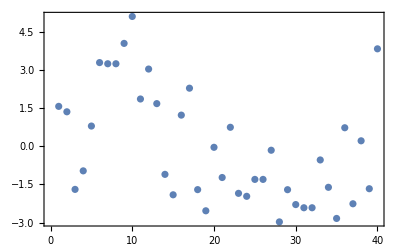
-Graphics-Variation in X (mm)Image Number

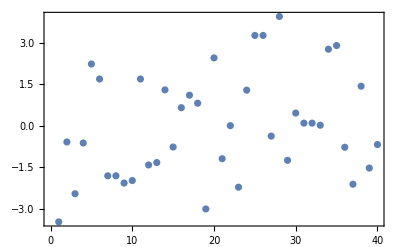
-Graphics-Variation in X (mm)Image Number

```mathematica
xPlot=ListPlot[xDiff,Frame->{True,True,False,False},Axes->False];plot1=Labeled[Labeled[xPlot,"Variation in X (mm)",{{Left,Center}}, RotateLabel->True], "Image Number", {{Bottom, Center}}]

yPlot=ListPlot[yDiff,Frame->{True,True,False,False},Axes->False];
plot2=Labeled[Labeled[yPlot,"Variation in X (mm)",{{Left,Center}}, RotateLabel->True], "Image Number", {{Bottom, Center}}]
```

### Now we can see visually the variation of the laser spot from the mean position on our images . You do not have a set of 40 images to do this with though . You will have a video of some length with some amount of frames . What you are going to want to do to extract data from your video is import your video, separate the video into an array of the frames (Not necessarily all of the frames, maybe one out of every 5 or 10 frames . This is a choice you will have to make and perhaps some trial and error will help you determine the best number of frames to include) Once you have an array of frames, you will then want to perform a similar task as demonstrated above . How do we import a video? Using Mathematica 13.1, you can do this as follows: First, I am going to just import the video. Then I am going to import the frames of the video separately.

```mathematica
videoMOV=Import["C:\\Users\\steve\\Downloads\\IMG_0855.MOV"]
videoFrames=Import["C:\\Users\\steve\\Downloads\\IMG_0855.MOV","ImageList"];
```

### Before doing anything else, I want to know how many frames I am working with and what the size of each image is.

```mathematica
Length[videoFrames]
ImageDimensions[videoFrames[[1]]]
```

257

{1920,1080}

### Each image is 1920 x1080 . Knowing this, I will now use the Manipulate function to play around and see where the import information in my video is stored.

```mathematica
Manipulate[ImageTake[videoFrames[[1]],{a,b},{c,d}],{a,1,1080},{b,2,1080},{c,1,1920},{d,2,1920}]
```

```mathematica
ImageTake[videoFrames[[1]],{100,600},{600,1200}]
```

-Graphics-

### After using Manipulate, you are going to want to go through and crop each image in your array of frames. We have previously done this though, so I am going to run through a couple steps here. For explanations of what I am doing, see above.

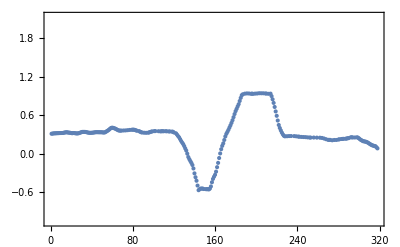
-Graphics-Variation in X (mm)Frame Number

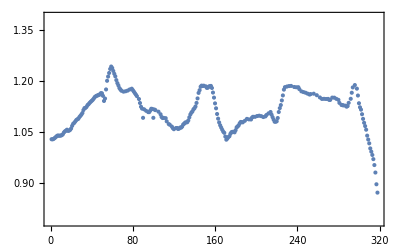
-Graphics-Variation in X (mm)Frame Number

```mathematica
For[i=1,i<= Length[videoFrames],i++,
cropped[[i]]=ImageTake[videoFrames[[i]],{100,600},{600,1200}];
cropped[[i]]=Binarize[cropped[[i]],0.45];
];
centers=Reap@For[i=1,i<=Length[cropped],i++,
Sow[ComponentMeasurements[cropped[[i]],"Centroid"]]
]//Last//First;
coords=centers//Values;
xvalues=Flatten[coords[[;;,;;,1]]];
yvalues=Flatten[coords[[;;,;;,2]]];
xmean=Mean[xvalues];
ymean=Mean[yvalues];
mean={xmean,ymean};
f[x_]:=x-xmean;
g[y_]:=y-ymean;
xdiff=f[xvalues];
ydiff=g[yvalues];

xplot=ListPlot[xdiff,Frame->{True,True,False,False},Axes->False];pLOT1=Labeled[Labeled[xplot,"Variation in X (mm)",{{Left,Center}}, RotateLabel->True], "Frame Number", {{Bottom, Center}}]

yplot=ListPlot[ydiff,Frame->{True,True,False,False},Axes->False];
pLOT2=Labeled[Labeled[yplot,"Variation in X (mm)",{{Left,Center}}, RotateLabel->True], "Frame Number", {{Bottom, Center}}]
```

```mathematica
cropped[[100]]
```

-Graphics-

```mathematica
Binarize[cropped[[1]],0.45]
```